### Сalculate the initial conditions for the first stage m'[x]==-u

```mathematica
Clear[all]
sol1=Flatten[Simplify[DSolve[{θ'[x]==ω[x],ω'[x]==m[x]+θ[x],m'[x]==-SubStar[u],θ[0]==1,ω[0]==Subscript[Ω, 0],m[0]==0},{θ[x],ω[x],m[x]},x]]]
```

{m[x]→-x u_*,θ[x]→1/2 ⅇ^-x (1+ⅇ^(2 x)+(-1+ⅇ^(2 x)) Ω_0+(1-ⅇ^(2 x)+2 ⅇ^x x) u_*),ω[x]→1/2 ⅇ^-x ((1+ⅇ^(2 x)) Ω_0-(-1+ⅇ^x) (-1-ⅇ^x+(-1+ⅇ^x) u_*))}

```mathematica
initForStage2={m[x]/.sol1⟦1⟧/.x->Subscript[τ, 1],θ[x]/.sol1⟦2⟧/.x->Subscript[τ, 1],ω[x]/.sol1⟦3⟧/.x->Subscript[τ, 1]}
```

{-τ_1 u_*,1/2 ⅇ^-τ_1 (1+ⅇ^(2 τ_1)+(-1+ⅇ^(2 τ_1)) Ω_0+(1-ⅇ^(2 τ_1)+2 ⅇ^τ_1 τ_1) u_*),1/2 ⅇ^-τ_1 ((1+ⅇ^(2 τ_1)) Ω_0-(-1+ⅇ^τ_1) (-1-ⅇ^τ_1+(-1+ⅇ^τ_1) u_*))}

### Сalculate the initial conditions for the second stage m'[x]==u

```mathematica
sol2=Flatten[Simplify[DSolve[{θ'[x]==ω[x],ω'[x]==m[x]+θ[x],m'[x]==SubStar[u],θ[Subscript[τ, 1]]==initForStage2[[2]],ω[Subscript[τ, 1]]==initForStage2[[3]],m[Subscript[τ, 1]]==initForStage2[[1]]},{θ[x],ω[x],m[x]},x]]]
```

{m[x]→(x-2 τ_1) u_*,θ[x]→1/2 (ⅇ^-x+ⅇ^x+(-ⅇ^-x+ⅇ^x) Ω_0+(ⅇ^-x-ⅇ^x+2 ⅇ^(x-τ_1)-2 ⅇ^(-x+τ_1)-2 x+4 τ_1) u_*),ω[x]→1/2 ⅇ^(-x-τ_1) (ⅇ^τ_1 (-1+ⅇ^(2 x))+ⅇ^τ_1 (1+ⅇ^(2 x)) Ω_0-(-2 ⅇ^(2 x)+ⅇ^τ_1-2 ⅇ^(2 τ_1)+2 ⅇ^(x+τ_1)+ⅇ^(2 x+τ_1)) u_*)}

### Сalculate the initial conditions for the third stage m'[x]==-u

```mathematica
sol3=Simplify[DSolve[{θ'[x]==ω[x],ω'[x]==m[x]+θ[x],m'[x]==-SubStar[u],θ[Subscript[τ, f]]==0,ω[Subscript[τ, f]]==0,m[Subscript[τ, f]]==0},{θ[x],ω[x],m[x]},x]]//Flatten
```

{m[x]→(-x+τ_f) u_*,θ[x]→1/2 (-ⅇ^(x-τ_f)+ⅇ^(-x+τ_f)+2 x-2 τ_f) u_*,ω[x]→-1/2 ⅇ^(-x-τ_f) (ⅇ^x-ⅇ^τ_f)^2 u_*}

```mathematica
linkingStage2={m[x]/.sol2⟦1⟧/.x->Subscript[τ, 2],θ[x]/.sol2⟦2⟧/.x->Subscript[τ, 2]//Simplify,ω[x]/.sol2⟦3⟧/.x->Subscript[τ, 2]//Simplify}
```

{(-2 τ_1+τ_2) u_*,1/2 (ⅇ^-τ_2+ⅇ^τ_2+(-ⅇ^-τ_2+ⅇ^τ_2) Ω_0+(-2 ⅇ^(τ_1-τ_2)+ⅇ^-τ_2-ⅇ^τ_2+2 ⅇ^(-τ_1+τ_2)+4 τ_1-2 τ_2) u_*),1/2 ⅇ^(-τ_1-τ_2) (ⅇ^τ_1 (-1+ⅇ^(2 τ_2))+ⅇ^τ_1 (1+ⅇ^(2 τ_2)) Ω_0-(ⅇ^τ_1-2 ⅇ^(2 τ_1)-2 ⅇ^(2 τ_2)+2 ⅇ^(τ_1+τ_2)+ⅇ^(τ_1+2 τ_2)) u_*)}

```mathematica
linkingStage3={m[x]/.sol3⟦1⟧/.x->Subscript[τ, 2],θ[x]/.sol3⟦2⟧/.x->Subscript[τ, 2]//Simplify,ω[x]/.sol3⟦3⟧/.x->Subscript[τ, 2]//Simplify}
```

{(-τ_2+τ_f) u_*,1/2 (-ⅇ^(τ_2-τ_f)+ⅇ^(-τ_2+τ_f)+2 τ_2-2 τ_f) u_*,-1/2 ⅇ^(-τ_2-τ_f) (ⅇ^τ_2-ⅇ^τ_f)^2 u_*}

```mathematica
first=(linkingStage2[[1]]-linkingStage3[[1]]==0//Simplify)
```

(2 τ_1-2 τ_2+τ_f) u_*==0

```mathematica
first1=z==y/x
```

z==y/x

```mathematica
second=(linkingStage2[[2]]-linkingStage3[[2]]==0//Simplify)
```

1/2 (ⅇ^-τ_2+ⅇ^τ_2+(-ⅇ^-τ_2+ⅇ^τ_2) Ω_0+(-2 ⅇ^(τ_1-τ_2)+ⅇ^-τ_2-ⅇ^τ_2+2 ⅇ^(-τ_1+τ_2)+ⅇ^(τ_2-τ_f)-ⅇ^(-τ_2+τ_f)+4 τ_1-4 τ_2+2 τ_f) u_*)==0

```mathematica
1/2 (1/y+y+(-1/y+y) Subscript[Ω, 0]+(-2 x/y+1/y-y+2 y/x+(y*x^2)/y^2-y^2/(x^2 y)) SubStar[u])==0
```

1/2 (1/y+y+(-1/y+y) Ω_0+(1/y-(2 x)/y+x^2/y-y-y/x^2+(2 y)/x) u_*)==0

```mathematica
second1=1/2 (1/y+y+(-1/y+y) Subscript[Ω, 0]+((-2x)/y+1/y-y+(2y)/x+(y*x^2)/y^2-y^2/(x^2 y)) SubStar[u])==0
```

1/2 (1/y+y+(-1/y+y) Ω_0+(1/y-(2 x)/y+x^2/y-y-y/x^2+(2 y)/x) u_*)==0

```mathematica
third=(linkingStage2[[3]]-linkingStage3[[3]]==0//Simplify)
```

1/2 ⅇ^-τ_2 (-1+ⅇ^(2 τ_2)+(1+ⅇ^(2 τ_2)) Ω_0+(-1+2 ⅇ^τ_1-4 ⅇ^τ_2-ⅇ^(2 τ_2)+2 ⅇ^(-τ_1+2 τ_2)+ⅇ^(2 τ_2-τ_f)+ⅇ^τ_f) u_*)==0

```mathematica
third1=1/2  1/y(-1+y^2+(1+y^2) Subscript[Ω, 0]+(-1+2 x-4 y-y^2+2 y^2/x+(y^2 x^2)/y^2+y^2/x^2) SubStar[u])==0
```

(-1+y^2+(1+y^2) Ω_0+(-1+2 x+x^2-4 y-y^2+y^2/x^2+(2 y^2)/x) u_*)/(2 y)==0

```mathematica
SubStar[t]=0.346; dt=0.25;SubStar[u]=1.65;Subscript[Ω, 0]=-SubStar[t]/dt;
Print["Ω_0=",Subscript[Ω, 0]]
```

Ω_0=-1.384

```mathematica
roots=FindRoot[{first,second,third},{Subscript[τ, 1],0.2},{Subscript[τ, 2],1.08},{Subscript[τ, f],1.76},MaxIterations->∞]
```

{τ_1→0.0771448,τ_2→0.903463,τ_f→1.65264}

```mathematica
Subscript[τ, 1]=roots[[1]][[2]];Subscript[τ, 2]=roots[[2]][[2]]; Subscript[τ, f]=roots[[3]][[2]];
```

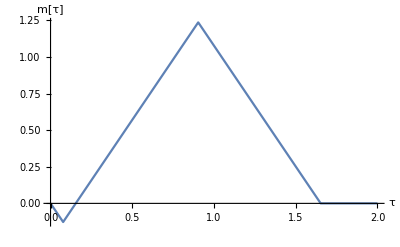

```mathematica
Plot[Piecewise[{{sol1[[1]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[1]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[1]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}],{x,0,2},AxesLabel->{Style["τ",17,Black],Style["m[τ]",17,Black]}]
```

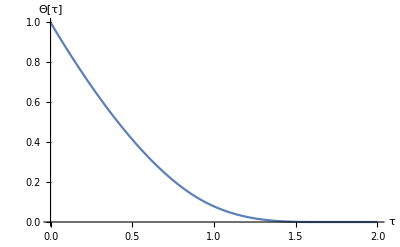

```mathematica
Plot[Piecewise[{{sol1[[2]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[2]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[2]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}],{x,0,2},AxesLabel->{Style["τ",17,Black],Style["Θ[τ]",17,Black]}]
```

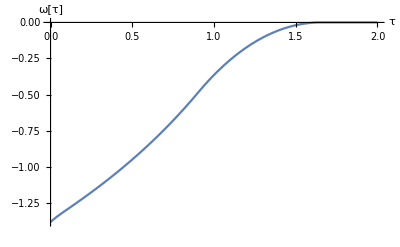

```mathematica
Plot[Piecewise[{{sol1[[3]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[3]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[3]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}],{x,0,2},AxesLabel->{Style["τ",17,Black],Style["ω[τ]",17,Black]}]
```